```mathematica
Exit[]
```

# Perturbation Theory

## Solving an IVP by perturbation methods

Consider the following equation

(d^2 x)/dt^2+dx/dt=-1/(1+ϵx)^2,          x(0)=0,     dx/dt(0)=1

```mathematica
eq=D[x[t],{t,2}]+D[x[t],t]+1/(1+ϵ x[t])^2
```

1/(1+ϵ x[t])^2+x'[t]+x''[t]

First, we find the center of perturbation by setting ϵ to zero and finding the corresponding solution to the IVP*

```mathematica
DSolve[{(eq/.ϵ->0)==0,x[0]==0,x'[0]==1},x[t],t]//Expand
```

{{x[t]→2-2 ⅇ^-t-t}}

This gives us the solution serving as the center of our perturbation

x_0=2-2 e^-t-t

We will now perturb the system by plugging in x_0+ ϵx_1+ ϵ^2 x_2 + ϵ^3 x_3+... by plugging the ansatz into the differential equation

```mathematica
p=eq/.x->Function[{t},2-2 ⅇ^-t-t+ϵ x1[t]+ϵ^2 x2[t]+O[ϵ]^3]
```

(-2 (2-2 ⅇ^-t-t)+x1'[t]+x1''[t]) ϵ+(1/2 (6 (2-2 ⅇ^-t-t)^2-4 x1[t])+x2'[t]+x2''[t]) ϵ^2+1/3 (-2 (2-2 ⅇ^-t-t) (6 (2-2 ⅇ^-t-t)^2-4 x1[t])+10 (2-2 ⅇ^-t-t) x1[t]-6 x2[t]) ϵ^3+O[ϵ]^4

We can analyze the coefficients of each epsilon powers using CoefficientList

```mathematica
plist=CoefficientList[p,ϵ]
```

{0,-2 (2-2 ⅇ^-t-t)+x1'[t]+x1''[t],1/2 (6 (2-2 ⅇ^-t-t)^2-4 x1[t])+x2'[t]+x2''[t],1/3 (-2 (2-2 ⅇ^-t-t) (6 (2-2 ⅇ^-t-t)^2-4 x1[t])+10 (2-2 ⅇ^-t-t) x1[t]-6 x2[t])}

```mathematica
{0,-2(2-2 ⅇ^-t-t),1/2 (6 (2-2 ⅇ^-t-t)^2-4 x1),1/3 (-2 (2-2 ⅇ^-t-t) (6 (2-2 ⅇ^-t-t)^2-4 x1)+10 (2-2 ⅇ^-t-t) x1-6 x2)}
```

Each coefficients of epsilon gives us a differential equation to solve serving as pieces of our final perturbative solution. We can call them one-by-one and then setting them to zero.

To find x_1, we solve the second element of the list.

```mathematica
DSolve[{plist[[2]]==0,x1[0]==0,x1'[0]==1},x1,t]//Simplify
```

{{x1→Function[{t},-ⅇ^-t (-9+9 ⅇ^t-4 t-6 ⅇ^t t+ⅇ^t t^2)]}}

To find x_2, we plug in x_1 to the third element and solve for x_2.

```mathematica
DSolve[{(plist[[3]]/.x1->Function[{t},-ⅇ^-t (-9+9 ⅇ^t-4 t-6 ⅇ^t t+ⅇ^t t^2)])==0,x2[0]==0,x2'[0]==2},x2,t]//Simplify
```

{{x2→Function[{t},-1/3 ⅇ^(-2 t) (18+276 ⅇ^t-294 ⅇ^(2 t)+114 ⅇ^t t+192 ⅇ^(2 t) t-6 ⅇ^t t^2-51 ⅇ^(2 t) t^2+5 ⅇ^(2 t) t^3)]}}

Then, the the perturbative solution is

```mathematica
s[ϵ_]:=2-2 ⅇ^-t-t+ϵ (-ⅇ^-t (-9+9 ⅇ^t-4 t-6 ⅇ^t t+ⅇ^t t^2))+ϵ^2 (-1/3 ⅇ^(-2 t) (18+276 ⅇ^t-294 ⅇ^(2 t)+114 ⅇ^t t+192 ⅇ^(2 t) t-6 ⅇ^t t^2-51 ⅇ^(2 t) t^2+5 ⅇ^(2 t) t^3))
```

While the numerical solution is

```mathematica
n[ϵ_]:=x[t]/.First@NDSolve[{D[x[t],{t,2}]+D[x[t],t]+1/(1+ϵ x[t])^2==0,x[0]==0,x'[0]==1},x,{t,0,10},WorkingPrecision->50];
```

Doing this by hand (using the table of approximations as guide), we can solve two sets of IVPs. Using a very simple linear ansatz

x=x_0+ϵ x_1

This will divide the IVP into two. The IVPs are not too difficult to solve.

The particular solution can be easily computed by its characteristic equation while undetermined coefficients will take care of the second differential equation.

```mathematica
DSolve[{D[x0[t],{t,2}]+D[x0[t],t]+1==0,x0[0]==0,x0'[0]==1},x0[t],t]
```

{{x0[t]→-ⅇ^-t (2-2 ⅇ^t+ⅇ^t t)}}

```mathematica
DSolve[{D[x1[t],{t,2}]+D[x1[t],t]-2(-ⅇ^-t (2-2 ⅇ^t+ⅇ^t t))==0,x1[0]==0,x1'[0]==0},x1[t],t]
```

{{x1[t]→-ⅇ^-t (-10+10 ⅇ^t-4 t-6 ⅇ^t t+ⅇ^t t^2)}}

```mathematica
h[ϵ_]:=-ⅇ^-t (2-2 ⅇ^t+ⅇ^t t)+ϵ (-ⅇ^-t (-10+10 ⅇ^t-4 t-6 ⅇ^t t+ⅇ^t t^2))
```

To compare, we can plot all solutions

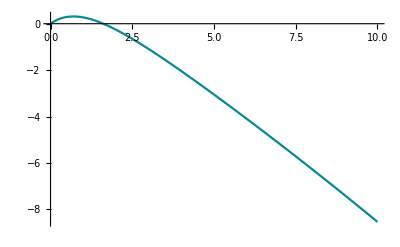

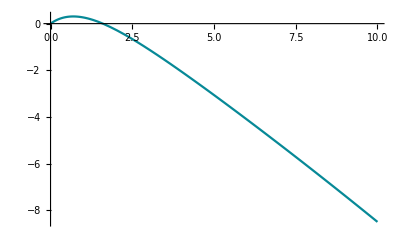

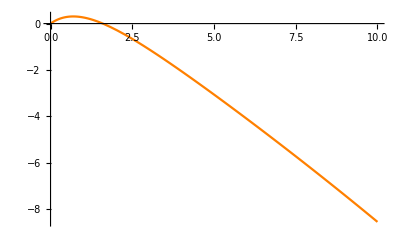

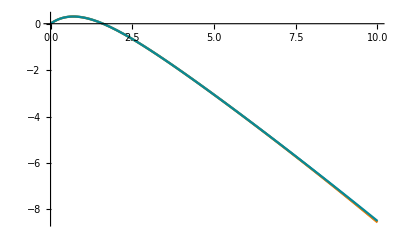

```mathematica
ps=Plot[s[1/100],{t,0,10}]
ph=Plot[h[1/100],{t,0,10}]
pn=Plot[Evaluate[n[1/100]],{t,0,10},PlotStyle->Orange]
Show[ps,pn,ph]
```

Observe that at this time scale, both approximations fit like a glove to the numerical ones.